```mathematica
Quit[];
```

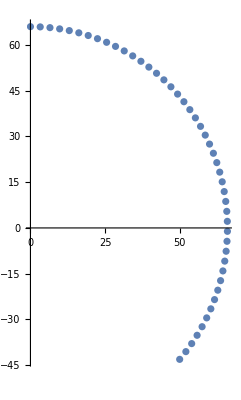

```mathematica
ListPlot[Transpose[{cx⟦1;;-1,1⟧,cy⟦1;;-1,1⟧}],AspectRatio->Automatic]
```

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
sp0=Import["sp0.txt","Table"];
n0 = (Length@sp0+1)/3;
cx=sp0⟦1;;n0⟧;
cy=sp0⟦n0+1;;n0*2⟧;
h=sp0⟦2 n0+1;;-1⟧;
(*Length@data*)
Subscript[sx, i_][t_?NumberQ]:=cx⟦i,1⟧+cx⟦i,2⟧t+(cx⟦i,3⟧t^2+cx⟦i,4⟧t^3+cx⟦i,5⟧t^4+cx⟦i,6⟧t^5)
Subscript[sy, i_][t_?NumberQ]:=cy⟦i,1⟧+cy⟦i,2⟧t+(cy⟦i,3⟧t^2+cy⟦i,4⟧t^3+cy⟦i,5⟧t^4+cy⟦i,6⟧t^5)
{x[t_],y[t_]}=50(1+0.05Cos[8t-π]){Sin[t],Cos[t]};
(*Table[{Subscript[sx, i][t],Subscript[sy, i][t]},{i,1,Length@cx-1}];
Show[
ListPlot[Transpose[{cx⟦1;;-1,1⟧,cy⟦1;;-1,1⟧}]]
,ParametricPlot[{%⟦1;;n0-1;;2⟧,%⟦2;;n0-1;;2⟧},{t,0,1},AspectRatio->Automatic,PlotStyle->{Blue,Red}]
,AspectRatio->Automatic,ImageSize->Medium]*)
```

2

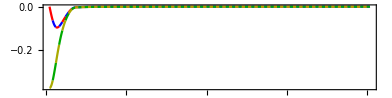

```mathematica
dv=2
tx = Table[Flatten@{#+i,Derivative[dv][Subscript[sx, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.1],{i,Range[1,n0-1]}];
ty = Table[Flatten@{#+i,Derivative[dv][Subscript[sy, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.1],{i,Range[1,n0-1]}];
(*ty = Table[{t+i,Derivative[dv][Subscript[sy, i]][t]/h⟦i⟧^dv},{i,1,Length@cx-1}];*)
Show[
ListPlot[tx,PlotStyle->{Red,Blue},Joined->True,PlotRange->All],
ListPlot[ty,PlotStyle->Darker@{Yellow,Green},Joined->True,PlotRange->All],
Axes->True,
(*ParametricPlot[{ty⟦1⟧,ty⟦2⟧},{t,0,1}],*)
AspectRatio->0.25,Frame->True,PlotRange->All]
```

{-0.0173991,-0.0172838,-0.0171701,-0.0170578,-0.016947,-0.0168376,-0.0167296,-0.016623,-0.0165177,-0.0164138,-0.0163111,-0.0162098,-0.0161097,-0.0160108,-0.0159131,-0.0158166,-0.0157213,-0.0156271,-0.0155341,-0.0154421,-0.0153512,-0.0152614,-0.0151726,-0.0150849,-0.0149982,-0.0149124,-0.0148276,-0.0147438,-0.014661,-0.014579,-0.014498,-0.0144179,-0.0143386,-0.0142602,-0.0141827,-0.014106,-0.0140301,-0.0139551,-0.0138808,-0.0138074,-0.0137347,-0.0136627,-0.0135915,-0.0135211,-0.0134514,-0.0133824,-0.0133141,-0.0132464,-0.0131795,-0.0131133}

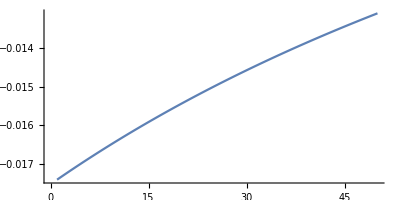

```mathematica
Clear[i,kv,kvt]
θ=Table[ArcCos[Subscript[sy, i][0]/√((Subscript[sx, i][0])^2+ (Subscript[sy, i][0])^2)],{i,1,Length@cx}];//Quiet;
Subscript[kv, i_][t_]:=(Subscript[sx, i]'[t]Subscript[sy, i]''[t]-Subscript[sy, i]'[t]Subscript[sx, i]''[t])/((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)^1.5+(Subscript[sy, i]'[t])/Subscript[sx, i][t]/√((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)
kvt[t_]:=(x'[t]y''[t]-y'[t]x''[t])/(x'[t]^2+y'[t]^2)^1.5
Table[Subscript[kv, i][0.],{i,n0-50,n0-1 }]
Show[ListPlot[%,PlotRange->All,Joined->True],AspectRatio->0.5]
```

```mathematica
6.219718254214801*^-7
```

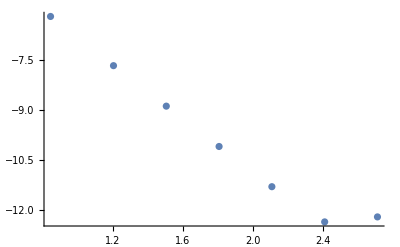

FittedModel[-3.59043-3.462 x]

```mathematica
dd={{7,6.219718254214801*^-7},
{16,2.1043927281305663*^-8},
{32,1.2964614815730302*^-9},
{64,8.074397574164838*^-11},
{128,5.0717728627969194*^-12},
{256,4.4955358879938956*^-13},
{512,6.340639818747107*^-13}
};
ListPlot@Log10@dd
LinearModelFit[Log10@dd,{x},x]
```

```mathematica
386*4
```

1544